## Jacobian of polar -> cartesian

```mathematica
absT[x_,y_]:=Sqrt[x^2+y^2]
argT[x_,y_]:=ArcTan[y/x]
Det[{{D[absT[x,y],x],D[argT[x,y],x]},{D[absT[x,y],y],D[argT[x,y],y]}}]//Simplify
```

1/(√(x^2+y^2))

## Flat prior on cartesian coordinates transformed to polar coordinates peaks at circle of radius 1

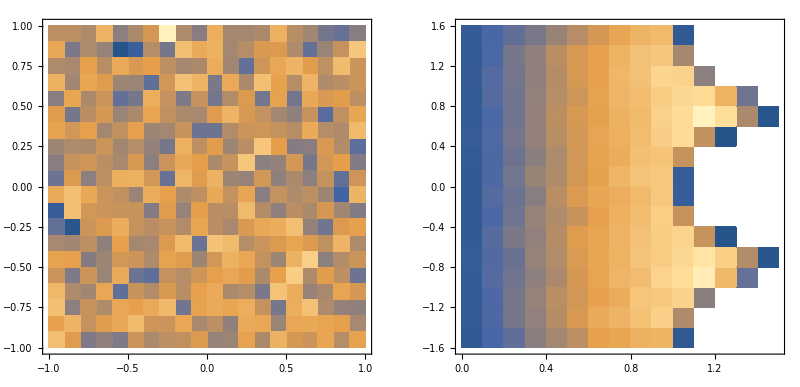

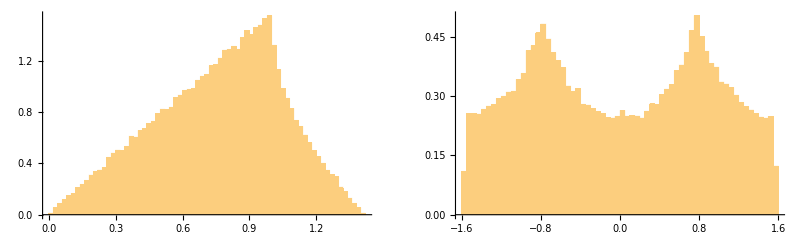

```mathematica
data=RandomReal[{-1,1},{100000,2}];
modulus = Sqrt[data[[All,1]]^2+data[[All,2]]^2];
phase =ArcTan[data[[All,2]] / data[[All,1]]];
GraphicsRow[{DensityHistogram[data],DensityHistogram[{modulus,phase}//Transpose]}]
GraphicsRow[Map[Histogram[#,"Scott","PDF"]&,{modulus,phase}]]
```

## Exact result: for every circle completely in the square, accumulated probability along the circle is proportional to the circumference or radius. For larger circles, there are 4 missing sectors, so the length inside is (2π-8ArcCos(1/(|z|))) |z|. Fix height by continuity at |z|=1 and normalization.

```mathematica
Solve[a absT==b (2Pi-8ArcCos[1/absT])absT/.absT->1,a]
```

{{a→2 b π}}

```mathematica
Solve[Integrate[Piecewise[{{2Pi b absT,absT≤1},{b(2Pi-8ArcCos[1/absT])absT,absT>1}}],{absT,0,√2}]==1,b]
```

{{b→1/4}}

Piecewise[{{(absT π)/2, absT≤1}, {1/4 absT (2 π-8 ArcCos[1/absT]), absT>1}, {0, True}}]

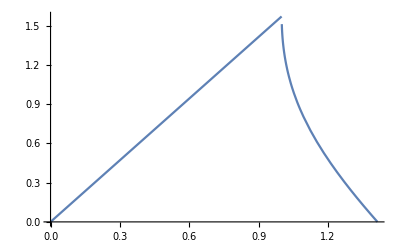

1

```mathematica
pdf=Piecewise[{{Pi/2 absT,absT≤1},{1/4(2Pi-8ArcCos[1/absT])absT,absT>1}}]
Plot[pdf,{absT,0,√2}]
Integrate[pdf,{absT,0,√2}]
```

## Flat prior on polar coordinates transformed to cartesian coordinates peaks at the origin

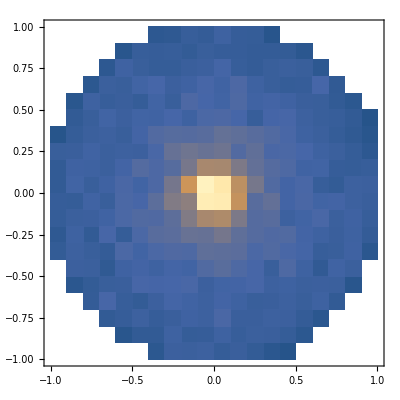

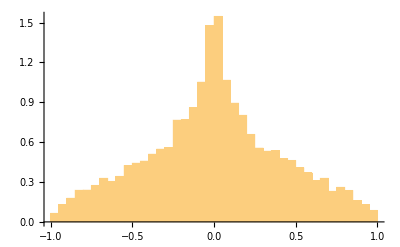

```mathematica
data={RandomReal[{0,1},10000], RandomReal[{0,2 Pi}, 10000]};
complex=data[[1,All]]*Exp[I data[[2,All]]];
cartesian={Re[complex],Im[complex]}//Transpose;
DensityHistogram[cartesian]
Histogram[cartesian[[All,1]],"Scott","PDF"]
```